```mathematica
(* Program to infer optimal eddy influence function *)

hmaxp=5180.72361835720; hminp=2.6 Sqrt[5186]; n=500; dhp=(hmaxp-hminp)/n;

Uinf=26.57528387419314;


Udns=Import["/Users/kdur/Matlab_Codes/AttachedEddy/500.txt","Table"];


A=Array[0&,{n+1,n+1}];
CF=Array[0&,{n+1,2n+1}];
IM=A;
Bp = Array[bp,2n+1];
Phphp2=Array[0&,n+1];
Uexp=Array[0&,n+1];
hp=Array[0&,n+1];

For[i=1,i≤n+1,i++,
hp[[i]]=hminp+dhp (i-1);]

For[i=1,i≤n+1,i++,
Phphp2[[i]]=2/(1/hminp^2-1/hmaxp^2)/hp[[i]];]
For[i=1,i≤n+1,i++,
Uexp[[i]]=Udns[[i,2]]-Uinf; 
]

(* The above is if we're inferring the mean streamwise eddy contribution function *)
(* Procedure for other functions is exactly the same. Just change the input data Udns *)

(* construct IM and use interpolation *)
For[i=1,i≤n+1,i++,
For[j=1,j≤n+1,j++,
A[[i,j]]= hp[[i]]/hp[[j]];]]

For[i=1,i≤n+1,i++,
IM[[i,1]]=Bp[[i]];
 IM[[i,i]]=Bp[[1]]];
For[i=2,i≤n+1,i++,
IM[[1,i]]=Bp[[n+i]]];

For[i=3,i≤n+1,i++,
For[j=2,j<i,j++,
k=1;ke=k; While[A[[k,1]]<A[[i,j]],ke=k;k++];
 frac=(A[[i,j]]-A[[ke,1]])/(A[[ke+1,1]]-A[[ke,1]]); 
 (* IM[[i,j]]=A[[ke,1]](1-frac)+A[[ke+1,1]]frac *); 
(* IM[[i,j]]=Bp[[ke]](1-frac)+Bp[[ke+1]]frac; *)
IM[[i,j]]=IM[[ke,1]](1-frac)+IM[[ke+1,1]]frac ;
]]


For[i=2,i≤n,i++,
For[j=i+1,j≤n+1,j++,
k=n+1;ke=k;While[A[[1,k]]<A[[i,j]],ke=k;k--];
frac=(A[[i,j]]-A[[1,ke]])/(A[[1,ke-1]]-A[[1,ke]]); 
 (* IM[[i,j]]=A[[1,ke]](1-frac)+A[[1,ke-1]]frac; *)
 IM[[i,j]]=IM[[1,ke]](1-frac)+IM[[1,ke-1]]frac; 
]]

(* Find coefficients *)

Eqn=Expand[IM.Phphp2 dhp-Uexp];

For[i=1,i≤n+1,i++,
For[j=1,j≤2 n+1,j++,
CF[[i,j]]=Coefficient[Eqn[[i]],bp[j]];]]

MatrixForm[CF];
BF=CF.Bp-Eqn;
BS=Transpose[CF].Inverse[CF.Transpose[CF]].BF;
For[j=1,j≤2 n+1,j++,
bp[j]=BS[[j]];
]
```

3

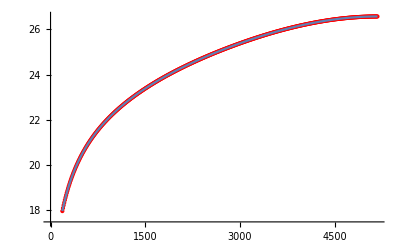

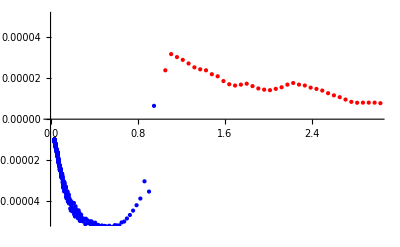

```mathematica
MatrixForm[IM];

dat1=Transpose@{hp,IM.Phphp2 dhp+Uinf};
dat2=Transpose@{hp,Uexp+Uinf};
Show[ListPlot[dat1,PlotStyle-> {PointSize[Large],Red}],ListPlot[dat2,Joined-> True]]
dat3=Transpose@{A[[1]],IM[[1]]};
dat4=Transpose@{A[[All,1]],IM[[All,1]]};
Show[ListPlot[dat3,PlotStyle-> {PointSize[Small],Blue}],ListPlot[dat4,PlotStyle-> {PointSize[Small],Red}],PlotRange-> {{0,3},{-0.00005,0.00005}}]
(* Output *)
Export["/Users/kdur/Matlab_Codes/AttachedEddy/I1.dat",dat3];
Export["/Users/kdur/Matlab_Codes/AttachedEddy/I2.dat",dat4];
```